# Test Problems for the GEP Algorithm

## 2D with pics

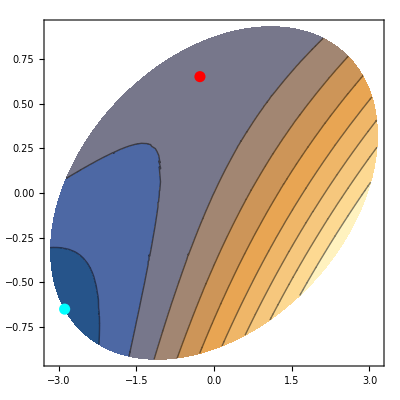

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
Δ=0.7;
Ω=ImplicitRegion[{x,y}.B.{x,y}≤Δ^2,{x,y}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
λs=Eigenvalues[{M0Twiddle,-M1Twiddle}];
λ=Re[Sort[λs,Re[#1]<Re[#2]&]⟦-1⟧];
pEdge=LinearSolve[A+λ B, -g];
ContourPlot[0.5*{x,y}.A.{x,y}+g.{x,y},{x,y}∈Ω,
Epilog->{
{Red,PointSize[0.02],Point[pCP]},
{Cyan, PointSize[0.02],Point[pEdge]}
}]
```

## 3D with pics

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
B=RandomReal[{-1,1},{m,m}];B=B.Bᵀ;
g=RandomReal[{-1,1},m];
f[p_]:=0.5p.A.p+g.p
Δ=0.7;
Ω=ImplicitRegion[{x,y,z}.B.{x,y,z}≤Δ^2,{x,y,z}];
{pStarBI}=NArgMin[{0.5*p.A.p+g.p,p.B.p≤Δ^2},p];
pCP=LinearSolve[A,-g];
M0=ArrayFlatten[({{{{Δ^2}}, 0, {g}}, {0, -B, A}, {{g}ᵀ, A, 0}})];
M1=ArrayFlatten[({{{{0}}, 0, 0}, {0, 0, B}, {0, B, 0}})];
M0Twiddle=ArrayFlatten[({{-B, A}, {A, -KroneckerProduct[g,g]/Δ^2}})];
M1Twiddle=ArrayFlatten[({{0, B}, {B, 0}})];
λs=Eigenvalues[{M0Twiddle,-M1Twiddle}];
λ=Re[Sort[λs,Re[#1]<Re[#2]&]⟦-1⟧];
pEdge=LinearSolve[A+λ B, -g];
Show[
ContourPlot3D[0.5*{x,y,z}.A.{x,y,z}+g.{x,y,z},{x,y,z}∈Ω,
Contours->7,PlotPoints->50,
PlotLegends->Automatic],
Graphics3D[{
{Red,PointSize[0.02],Point[pCP]},
{Cyan, PointSize[0.02],Point[pEdge]}
}]
]
TableForm[{
Map[FullForm[0.5 #.A.# + g.# ]&,{pCP,pEdge,pStarBI}],
Map[#.B.# -Δ^2 &,{pCP,pEdge,pStarBI}]
},TableHeadings->{{"f","cons"},{"pCP","pEdge","pStarBI"}}]
```

-Graphics3D-

| pCP | pEdge | pStarBI
f | -0.605193 | -1.07757 | -1.07757
cons | 2.15003 | -2.77556×10^-16 | -5.55112×10^-17